```mathematica
Integrate[Exp[-x^3],{x,0,Infinity}]
```

Gamma[4/3]

```mathematica
Gamma[4/3]//N
```

0.89298

```mathematica
(1/3)*Gamma[1/3]//N
```

0.89298

```mathematica
Integrate[Exp[x^3],{x,0,Infinity*ⅈ}]
```

-(ⅈ π)/Gamma[-1/3]+1/6 Gamma[1/3]

```mathematica
ans=Integrate[Exp[a*z^3/2],{z,0,Infinity*ⅈ},Assumptions->a>0]
hans=Im[ans]
```

-(2 (-2)^(1/3) π)/(√3 a^(1/3) Gamma[-1/3])

-(2 π Im[(-2)^(1/3)/a^(1/3)])/(√3 Gamma[-1/3])

```mathematica
ansa = ans/.a->1
```

-(2 (-2)^(1/3) π)/(√3 Gamma[-1/3])

```mathematica
ansa//N
```

0.562542+0.974351 ⅈ

```mathematica
ans2=Integrate[Exp[(z^3/2)],{z,0,Infinity*ⅈ}]
```

(-(2 ⅈ π)/Gamma[-1/3]+Gamma[4/3])/2^(2/3)

```mathematica
ans2//N
```

0.562542+0.974351 ⅈ

```mathematica
ans3=Integrate[Exp[a*(3*z^2/2)],{z,0,Infinity*ⅈ},Assumptions->a>0]
```

(ⅈ √(π/6))/(√a)

```mathematica
ans5=Integrate[Exp[a*(z^3/2+3*z^2/2)],{z,0,Infinity*ⅈ},Assumptions->a>0]
```

1/9 (√3 ⅇ^a (π BesselI[-1/3,a]+π BesselI[1/3,a]+3 ⅈ BesselK[1/3,a])-9 HypergeometricPFQ[{1/2,1},{2/3,4/3},2 a])

```mathematica
Im[ans5]//N
```

0.111111 Im[1.73205 2.71828^a (3.14159 BesselI[-0.333333,a]+3.14159 BesselI[0.333333,a]+(0.+3. ⅈ) BesselK[0.333333,a])-9. HypergeometricPFQ[{0.5,1.},{0.666667,1.33333},2. a]]

```mathematica
favolla[a_]:=Im[Integrate[Exp[a*(z^3/2+3*z^2/2)],{z,0,Infinity*ⅈ},Assumptions->a>0]]
```

```mathematica
favolla[0.25]
```

1.27101

```mathematica
decay[beta_,L_]:=L*Exp[1]*favolla[beta]
```

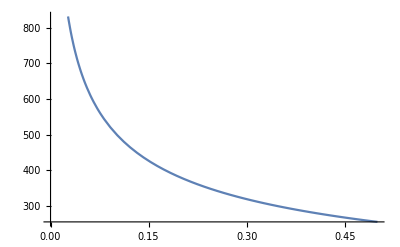

```mathematica
Plot[decay[beta,100],{beta,0,0.5}]
```

```mathematica
barrier=Import["C:\\trial_for\\Python_code\\barrier.txt","Table"];
```

```mathematica
barrier
```

{{1.},{0.953783127795123531},{0.907796524744142297},{0.868041384631747959},{0.85425294372105065},{0.886959830670440375},{0.976166585923353147},{1.12237169297436279},{1.32090899754528501},{1.56520989389849019},{1.84855582595505652},{2.16483893214524414},{2.5088019370950434},{2.87603973051595485},{3.26290785460420318},{3.66640587448072974},{4.08406454887880699},{4.51384723146254707},{4.95406771413629343},{5.40332339499420833},{5.86044155691038071},{6.32443640715708888},{6.79447476358331759},{7.26984861487183132},{7.74995312078344423},{8.23426891308494646},{8.72234780004470167},{9.21380117052079406},{9.70829054542299907},{10.2055198428134766},{10.7052290152763732},{11.2071887902591101},{11.7111963004337962},{12.2170714352632395},{12.7246537795864327},{13.0951476226788799},{13.5733259816587371},{14.0528236345866677},{14.5335350138571595},{15.01536473672647},{15.4982264424712835},{15.9820417842481728},{16.4667395518239488},{16.9522549055729144},{17.4385287055142833},{17.7758347147306459},{18.2384846770941884},{18.7017614962504517},{19.1656227051508381},{19.630029283955956},{20.0949453364859494},{20.5603378011939881},{21.0261761925306985},{21.4924323691211647},{21.9590803256462479},{22.4260960057198489},{22.8934571333973338},{23.3611430612439897},{23.8291346331470884},{24.2974140602744448},{24.7659648087729103},{25.2347714979658768},{25.7038198079533089},{26.1730963956435758},{26.6425888183567636},{26.8866922678985745},{27.3397503788709599},{27.793051635775317},{28.2465865888579089},{28.7003464166329145},{29.1543228798868306},{29.6085082794917796},{30.0628954176764793},{30.5174775624386427},{30.9722484148148922},{31.4272020787521029},{31.8823330333493686},{32.3376361072623411},{32.7931064550817837},{33.2487395355164068},{33.7045310912256326},{34.1604771301632724},{34.6165739083051918},{35.0728179136465172},{35.5292058513637912},{35.9857346300475669},{36.4424013489187431},{36.8992032859503283},{37.3561378868229355},{37.8132027546482803},{38.2703956404014249},{38.7277144340068844},{39.1851571560285521},{39.6427219499181689},{40.100407074779838},{40.5582108986127494},{41.0161318919964799},{41.4741686221866814},{41.9323197475912366},{42.3905840125998878},{42.8489602427415761},{43.3074473401468723},{43.7660442792937872},{44.224750103017314},{44.6835639187644773},{45.1424848950782121},{45.6015122582943349},{46.0606452894374598},{46.5198833213023448},{46.9792257357084182},{47.4386719609163663},{47.8982214691957182},{48.3578737745338998},{48.8176284304776971},{49.2774850280985817},{49.7374431940739896},{50.1975025888772208},{50.6576629050694791},{51.1179238656872599},{51.5782852227195221}}

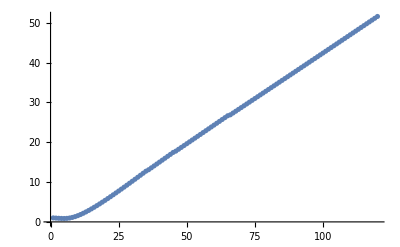

```mathematica
ListPlot[Flatten[barrier]]
```

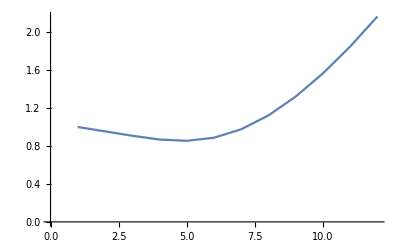

```mathematica
ListLinePlot[Flatten[barrier][[1;;12]]]
```

```mathematica
temp=Range[0,1,1/119];
```

```mathematica
Length[temp]
```

120

```mathematica
data=Transpose[{temp[[2;;36]],Exp[-(Flatten[barrier][[2;;36]]/25 )*(1/temp[[2;;36]] )]  }];
```

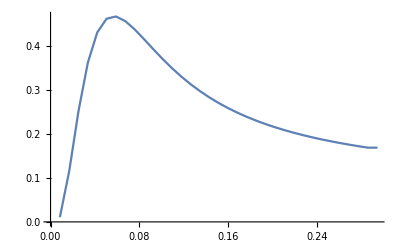

```mathematica
ListLinePlot[data]
```

```mathematica
ans9=Integrate[Exp[a*((t*(Cos[π/3]+ⅈ*Sin[π/3]))^3/2+3*(t*(Cos[π/3]+ⅈ*Sin[π/3])^2/2))],{t,0,Infinity},Assumptions->a>0]
```

((-1)^(1/3) MeijerG[{{1},{}},{{1/3,2/3,1},{}},-(-1/2)^(2/3) a^(2/3),1/3])/(√3 a π)

```mathematica
favolla[a_]:=Im[Integrate[Exp[a*((t*(Cos[π/3]+ⅈ*Sin[π/3]))^3/2+3*(t*(Cos[π/3]+ⅈ*Sin[π/3])^2/2))],{t,0,Infinity},Assumptions->a>0]]
```

```mathematica
decay1[beta_,L_]:=L*Exp[-beta]*favolla[beta]
```

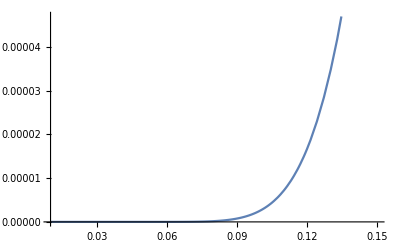

```mathematica
Plot[decay1[(1/temp),1],{temp,0.01,0.15}]
```

```mathematica
favollalagrange[a_]:=Im[Integrate[Exp[a*((t*(Cos[π/3]+ⅈ*Sin[π/3]))^3/2+3*(t*(Cos[π/3]+ⅈ*Sin[π/3])^2/2))],{t,0,Infinity},Assumptions->a>0]]
```

```mathematica
decay2[beta_,L_]:=L*Exp[-beta]*favollalagrange[beta]
```

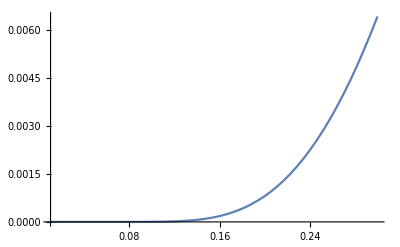

```mathematica
Plot[decay2[(1/temp),1],{temp,0.01,0.3}]
```